Classical detection problem between two Gaussian models. One having mean μ (stimulus present) and other with mean 0 (stimulus absent). Both have variance 1.
Let f be the reward per unit for false alarming (f < 0).
Let h be the reward per unit for getting a hit (f < 0).
We assume there is a cost for having a certain μ

```mathematica
Q[x_]:=1/2 Erfc[x/Sqrt[2]]
```

```mathematica
reward = h * Q[η-μ]+f Q[η]-μ;
```

```mathematica
Solve[D[reward,η]==0 && f<0 && h>0,η,Reals]
```

{{η→ConditionalExpression[-(-μ^2-2 Log[-f/h])/(2 μ), f<0&&h>0]}}

```mathematica
D[reward,μ]
```

-1+(ⅇ^(-1/2 (η-μ)^2) h)/(√(2 π))

```mathematica
2 Log[ (√(2 π))/h]+(η-μ)^2= 0
```

```mathematica
(2 Log[ (√(2 π))/h]+(η-μ)^2)/.{η-> -(-μ^2-2 Log[-f/h])/(2 μ)}//Simplify
```

2 Log[1/h]+((μ^2-2 Log[-f/h])^2)/(4 μ^2)+Log[2 π]

Once again assuming μ ≠ 0 (although we might have made this assumption before while calculating η).

```mathematica
μSols = μ/.Solve[2*4 μ^2 Log[1/h]+(μ^2-2 Log[-f/h])^2+Log[2 π]4 μ^2==0 ,μ,Reals];
ηSols=(-(-μ^2-2 Log[-f/h])/(2 μ))/.{μ-> μSols};
rewardSols=reward/.{μ-> μSols, η-> ηSols};
```

```mathematica
plots=Manipulate[Plot[#,{h,0.01,5}]&/@rewardSols,{{f, -8.6},-10,-.001}];
Show[plots]
```

Show::gtype: Manipulate is not a type of graphics.

Show[]

```mathematica
(*positiveElements=Select[abc,μ/. #>0&];*)
```

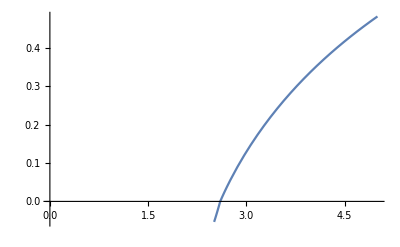
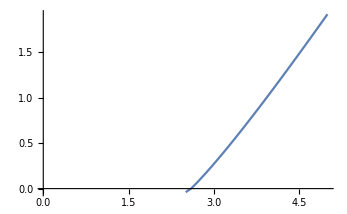
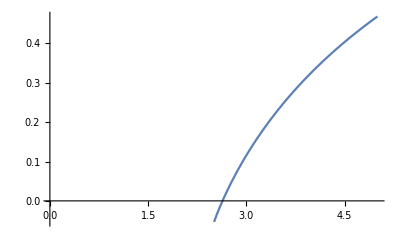
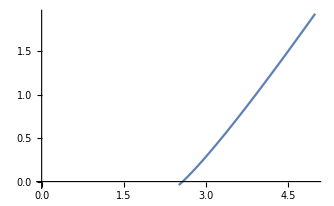

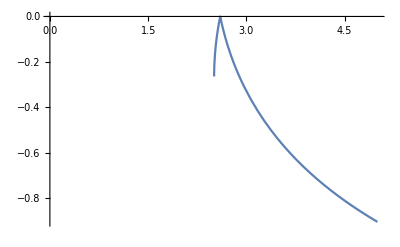
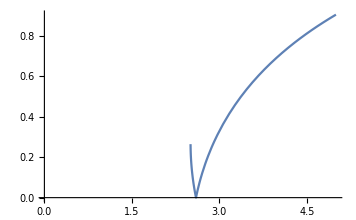
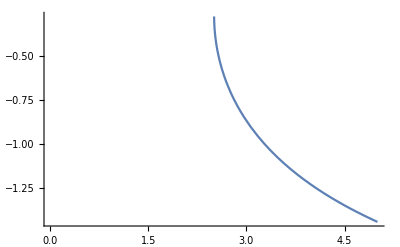
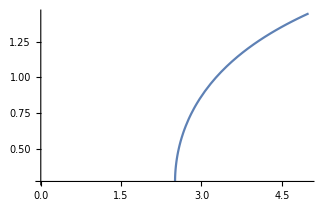

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot[#/.{f-> -2.6},{h,0.01,5}]&/@rewardSols
Plot[#/.{f-> -2.6},{h,0.01,5}]&/@μSols
Plot[#/.{f-> -2.6},{h,0.01,5}]&/@ηSols
```

```mathematica
Length[rewardSols]
```

4

```mathematica
μSols
```

{{μ→ConditionalExpression[-√(-2 (Log[2]+2 Log[1/h]-Log[-f/h]+Log[π])-2 √(4 Log[1/h]^2-4 Log[1/h] Log[-f/h]+4 Log[1/h] (Log[2]+Log[π])-2 Log[-f/h] (Log[2]+Log[π])+(Log[2]+Log[π])^2)), ]},{μ→ConditionalExpression[√(-2 (Log[2]+2 Log[1/h]-Log[-f/h]+Log[π])-2 √(4 Log[1/h]^2-4 Log[1/h] Log[-f/h]+4 Log[1/h] (Log[2]+Log[π])-2 Log[-f/h] (Log[2]+Log[π])+(Log[2]+Log[π])^2)), ]},{μ→ConditionalExpression[-√(-2 (Log[2]+2 Log[1/h]-Log[-f/h]+Log[π])+2 √(4 Log[1/h]^2-4 Log[1/h] Log[-f/h]+4 Log[1/h] (Log[2]+Log[π])-2 Log[-f/h] (Log[2]+Log[π])+(Log[2]+Log[π])^2)), ]},{μ→ConditionalExpression[√(-2 (Log[2]+2 Log[1/h]-Log[-f/h]+Log[π])+2 √(4 Log[1/h]^2-4 Log[1/h] Log[-f/h]+4 Log[1/h] (Log[2]+Log[π])-2 Log[-f/h] (Log[2]+Log[π])+(Log[2]+Log[π])^2)), ]}}

```mathematica
Length[μSols]
```

4

```mathematica
μSols = Flatten[Solve[2*4 μ^2 Log[1/h]+(μ^2-2 Log[-f/h])^2+Log[2 π]4 μ^2==0 ,μ,Reals]];
ηSols=(ConditionalExpression[-(-μ^2-2 Log[-f/h])/(2 μ), f<0&&h>0])/.μSols;
Length[μSols]
Length[ηSols]
μSols/.{f-> -2.76,h -> 3.3}
ηSols/.{f-> -2.76,h -> 3.3}
```

4

2

{μ→-0.302754,μ→0.302754,μ→-1.18044,μ→1.18044}

0.438844

```mathematica
μSols/.{f-> -2.76,h -> 3.3}
ηSols/.{f-> -2.76,h -> 3.3}
rewardSols/.{f-> -2.76,h -> 3.3}
```

{-0.302754,0.302754,-1.18044,1.18044}

{0.438844,-0.438844,-0.438844,0.438844}

{0.147131,0.392869,0.088557,0.451443}

```mathematica
μSols/.{f-> -2.76, h-> 2.6}
```

{-0.168389,0.168389,-0.709299,0.709299}

```mathematica
rewardSols/.{f-> -2.76, h-> 2.6}
```

{-0.102595,-0.0574046,-0.115979,-0.0440212}

```mathematica
Manipulate[Plot[{rewardSols[[1]]/.{f-> ftmp},rewardSols[[2]]/.{f-> ftmp},rewardSols[[3]]/.{f-> ftmp},rewardSols[[4]]/.{f-> ftmp}},{h,0.01,10},PlotLegends->Automatic],{{ftmp, -8.6},-10,-.001}]
```

```mathematica
Manipulate[Plot[{μSols[[1]]/.{f-> ftmp},μSols[[2]]/.{f-> ftmp},μSols[[3]]/.{f-> ftmp},μSols[[4]]/.{f-> ftmp}},{h,0.01,500},PlotLegends->Automatic],{{ftmp, -8.6},-10,-.001}]
```

```mathematica
Manipulate[Plot[{ηSols[[1]]/.{f-> ftmp},ηSols[[2]]/.{f-> ftmp},ηSols[[3]]/.{f-> ftmp},ηSols[[4]]/.{f-> ftmp}},{h,0.01,5},PlotLegends->Automatic],{{ftmp, -8.6},-10,-.001}]
```

```mathematica
Manipulate[Plot[{f Q[η]/.{η-> ηSols[[4]]}/.{f-> ftmp}, h Q[η]/.{η-> ηSols[[4]]}/.{f-> ftmp}},{h,0.01,20},PlotLegends->Automatic],{{ftmp, -8.6},-10,-.001}]
```

```mathematica
Manipulate[Plot[{f Q[η]/.{η-> ηSols[[4]]}/.{f-> ftmp},(h * Q[η-μ])/.{μ -> μSols[[4]],η-> ηSols[[4]]}/.{f-> ftmp},μ/.{μ -> μSols[[4]]}/.{f-> ftmp}},{h,0.01,5},PlotLegends->Automatic],{{ftmp, -8.6},-10,-.001}]
```

```mathematica
Manipulate[Plot[{f Q[η]/.{η-> ηSols[[4]]}/.{f-> ftmp}},{h,0.01,1000000},PlotLegends->Automatic],{{ftmp, -8.6},-10,-.001}]
```

```mathematica
Manipulate[Plot[{-(f Q[η]-μ)/.{μ-> μSols[[4]],η-> ηSols[[4]]}/.{f-> ftmp},(h * Q[η-μ])/.{μ -> μSols[[4]],η-> ηSols[[4]]}/.{f-> ftmp}},{h,0.01,5},PlotLegends->Automatic],{{ftmp, -8.6},-10,-.001}]
```

```mathematica
Manipulate[Plot3D[{h * Q[η-μ]+f Q[η]-μ},{η,-10,10},{μ,0,10},PlotLegends->Automatic,AxesLabel->Automatic],{{f, -8.6},-10,-.001},{{h, 8.6},.001,10}]
```

```mathematica
Manipulate[Plot3D[{h * Q[η-μ]},{η,-10,10},{μ,0,10},PlotLegends->Automatic,AxesLabel->Automatic],{{f, -8.6},-10,-.001},{{h, 8.6},.001,10}]
```

```mathematica
Manipulate[Plot3D[{h * Q[η-μ]+f Q[η]},{η,-10,10},{μ,0,10},PlotLegends->Automatic,AxesLabel->Automatic],{{f, -8.6},-20,-.001},{{h, 8.6},.001,20}]
```

```mathematica
Manipulate[Plot3D[{h * Q[η-μ],f Q[η]},{η,-10,10},{μ,0,10},PlotLegends->Automatic,AxesLabel->Automatic],{{f, -8.6},-10,-.001},{{h, 8.6},.001,10}]
```

```mathematica
h * Q[η-μ]+f Q[η]-μ
```

```mathematica
Manipulate[Plot[{ηSols[[4]]/.{f-> ftmp}},{h,0.01,5},PlotLegends->Automatic],{{ftmp, -8.6},-10,-.001}]
```

```mathematica
ηSols[[4]]//Simplify
```

ConditionalExpression[(-2 Log[1/h]+2 Log[-f/h]+Log[1/(2 π)]+√((2 Log[1/h]+Log[2 π]) (2 Log[1/h]-2 Log[-f/h]+Log[2 π])))/(√2 √(-2 Log[1/h]+Log[-f/(2 h π)]+√((2 Log[1/h]+Log[2 π]) (2 Log[1/h]-2 Log[-f/h]+Log[2 π])))), ]

```mathematica
Manipulate[Plot[{ηSols[[4]]/.{f-> ftmp}},{h,0.01,5},PlotLegends->Automatic],{{ftmp, -8.6},-10,-.001}]
```

```mathematica
(*Define the function*)objectiveFunction[h_,f_,η_,μ_]:=h*Q[η-μ]+f*Q[η]-μ

(*Specify the values of h and f for which you want to minimize the function*)
hValues={3,4,5};  (*Replace with your desired values*)
fValues={-6,-5,-4};  (*Replace with your desired values*)

(*Perform the numerical minimization for each combination of h and f*)
minimizationResults=Table[NMinimize[{objectiveFunction[h,f,η,μ],η∈Reals,μ∈Reals},{η,μ}],{h,hValues},{f,fValues}];

(*Extract the minimum values and corresponding values of η and μ*)
minValues=minimizationResults[[All,All,1]];
minArg=minimizationResults[[All,All,2]];

(*Create a 3D plot*)
ListPointPlot3D[Flatten[Table[{{h,f},minValues[[hIdx,fIdx]]},{hIdx,Length[hValues]},{fIdx,Length[fValues]}],1],PlotLabel->"Minimized Values of the Objective Function",AxesLabel->{"h","f","Minimum Value"},PlotRange->All]
```

ListPointPlot3D::ldata: {{{h,f},-2.69674},{{h,f},-1.80225},{{h,f},-0.943153},{{h,f},-2.48541},{{h,f},-1.59093},{{h,f},-0.731824},{{h,f},-2.34451},{{h,f},-1.45003},{{h,f},-0.590925}} is not a valid dataset or list of datasets.

ListPointPlot3D[{{{h,f},-2.69674},{{h,f},-1.80225},{{h,f},-0.943153},{{h,f},-2.48541},{{h,f},-1.59093},{{h,f},-0.731824},{{h,f},-2.34451},{{h,f},-1.45003},{{h,f},-0.590925}},PlotLabel→Minimized Values of the Objective Function,AxesLabel→{h,f,Minimum Value},PlotRange→All]

```mathematica
(*Define the function*)objectiveFunction[h_,f_,η_,μ_]:=h*Q[η-μ]+f*Q[η]-μ

(*Specify the values of h and f for which you want to minimize the function*)
hValues={3,4,5};  (*Replace with your desired values*)
fValues={-6,-5,-4};  (*Replace with your desired values*)
```

```mathematica
(*Perform the numerical minimization for each combination of h and f*)
minimizationResults=Table[NMaximize[{objectiveFunction[h,f,η,μ],η∈Reals,μ∈Reals},{η,μ}],{h,hValues},{f,fValues}];
```

```mathematica
minimizationResults
```

{{{-0.303263,{η→1.32123,μ→1.92068}},{-0.197746,{η→1.17516,μ→1.77462}},{-0.0568473,{η→0.966805,μ→1.56626}}},{{0.485408,{η→1.32123,μ→2.28803}},{0.590925,{η→1.17516,μ→2.14196}},{0.731824,{η→0.966805,μ→1.93361}}},{{1.34451,{η→1.32123,μ→2.49639}},{1.45003,{η→1.17516,μ→2.35032}},{1.59093,{η→0.966805,μ→2.14196}}}}

```mathematica
ListPointPlot3D[Flatten[Table[{{h,f},minimizationResults},{hIdx,Length[hValues]},{fIdx,Length[fValues]}],1],PlotLabel->"Minimized Values of the Objective Function",AxesLabel->{"h","f","Minimum Value"},PlotRange->All]
```

ListPointPlot3D::ldata: {«1»} is not a valid dataset or list of datasets.

ListPointPlot3D[{{{h,f},{{{-0.303263,{η→1.32123,μ→1.92068}},{-0.197746,{η→1.17516,μ→1.77462}},{-0.0568473,{η→0.966805,μ→1.56626}}},{{0.485408,{η→1.32123,μ→2.28803}},{0.590925,{η→1.17516,μ→2.14196}},{0.731824,{η→0.966805,μ→1.93361}}},{{1.34451,{η→1.32123,μ→2.49639}},{1.45003,{η→1.17516,μ→2.35032}},{1.59093,{η→0.966805,μ→2.14196}}}}},{{h,f},{{{-0.303263,{η→1.32123,μ→1.92068}},{-0.197746,{η→1.17516,μ→1.77462}},{-0.0568473,{η→0.966805,μ→1.56626}}},{{0.485408,{η→1.32123,μ→2.28803}},{0.590925,{η→1.17516,μ→2.14196}},{0.731824,{η→0.966805,μ→1.93361}}},{{1.34451,{η→1.32123,μ→2.49639}},{1.45003,{η→1.17516,μ→2.35032}},{1.59093,{η→0.966805,μ→2.14196}}}}},{{h,f},{{{-0.303263,{η→1.32123,μ→1.92068}},{-0.197746,{η→1.17516,μ→1.77462}},{-0.0568473,{η→0.966805,μ→1.56626}}},{{0.485408,{η→1.32123,μ→2.28803}},{0.590925,{η→1.17516,μ→2.14196}},{0.731824,{η→0.966805,μ→1.93361}}},{{1.34451,{η→1.32123,μ→2.49639}},{1.45003,{η→1.17516,μ→2.35032}},{1.59093,{η→0.966805,μ→2.14196}}}}},{{h,f},{{{-0.303263,{η→1.32123,μ→1.92068}},{-0.197746,{η→1.17516,μ→1.77462}},{-0.0568473,{η→0.966805,μ→1.56626}}},{{0.485408,{η→1.32123,μ→2.28803}},{0.590925,{η→1.17516,μ→2.14196}},{0.731824,{η→0.966805,μ→1.93361}}},{{1.34451,{η→1.32123,μ→2.49639}},{1.45003,{η→1.17516,μ→2.35032}},{1.59093,{η→0.966805,μ→2.14196}}}}},{{h,f},{{{-0.303263,{η→1.32123,μ→1.92068}},{-0.197746,{η→1.17516,μ→1.77462}},{-0.0568473,{η→0.966805,μ→1.56626}}},{{0.485408,{η→1.32123,μ→2.28803}},{0.590925,{η→1.17516,μ→2.14196}},{0.731824,{η→0.966805,μ→1.93361}}},{{1.34451,{η→1.32123,μ→2.49639}},{1.45003,{η→1.17516,μ→2.35032}},{1.59093,{η→0.966805,μ→2.14196}}}}},{{h,f},{{{-0.303263,{η→1.32123,μ→1.92068}},{-0.197746,{η→1.17516,μ→1.77462}},{-0.0568473,{η→0.966805,μ→1.56626}}},{{0.485408,{η→1.32123,μ→2.28803}},{0.590925,{η→1.17516,μ→2.14196}},{0.731824,{η→0.966805,μ→1.93361}}},{{1.34451,{η→1.32123,μ→2.49639}},{1.45003,{η→1.17516,μ→2.35032}},{1.59093,{η→0.966805,μ→2.14196}}}}},{{h,f},{{{-0.303263,{η→1.32123,μ→1.92068}},{-0.197746,{η→1.17516,μ→1.77462}},{-0.0568473,{η→0.966805,μ→1.56626}}},{{0.485408,{η→1.32123,μ→2.28803}},{0.590925,{η→1.17516,μ→2.14196}},{0.731824,{η→0.966805,μ→1.93361}}},{{1.34451,{η→1.32123,μ→2.49639}},{1.45003,{η→1.17516,μ→2.35032}},{1.59093,{η→0.966805,μ→2.14196}}}}},{{h,f},{{{-0.303263,{η→1.32123,μ→1.92068}},{-0.197746,{η→1.17516,μ→1.77462}},{-0.0568473,{η→0.966805,μ→1.56626}}},{{0.485408,{η→1.32123,μ→2.28803}},{0.590925,{η→1.17516,μ→2.14196}},{0.731824,{η→0.966805,μ→1.93361}}},{{1.34451,{η→1.32123,μ→2.49639}},{1.45003,{η→1.17516,μ→2.35032}},{1.59093,{η→0.966805,μ→2.14196}}}}},{{h,f},{{{-0.303263,{η→1.32123,μ→1.92068}},{-0.197746,{η→1.17516,μ→1.77462}},{-0.0568473,{η→0.966805,μ→1.56626}}},{{0.485408,{η→1.32123,μ→2.28803}},{0.590925,{η→1.17516,μ→2.14196}},{0.731824,{η→0.966805,μ→1.93361}}},{{1.34451,{η→1.32123,μ→2.49639}},{1.45003,{η→1.17516,μ→2.35032}},{1.59093,{η→0.966805,μ→2.14196}}}}}},PlotLabel→Minimized Values of the Objective Function,AxesLabel→{h,f,Minimum Value},PlotRange→All]

```mathematica
data={{{-0.303263,{η->1.32123,μ->1.92068}},{-0.197746,{η->1.17516,μ->1.77462}},{-0.0568473,{η->0.966805,μ->1.56626}}},{{0.485408,{η->1.32123,μ->2.28803}},{0.590925,{η->1.17516,μ->2.14196}},{0.731824,{η->0.966805,μ->1.93361}}},{{1.34451,{η->1.32123,μ->2.49639}},{1.45003,{η->1.17516,μ->2.35032}},{1.59093,{η->0.966805,μ->2.14196}}}};

ListPointPlot3D[Flatten[Table[{{h,f},minValues[[hIdx,fIdx,1]]},{hIdx,Length[hValues]},{fIdx,Length[fValues]}],1],PlotLabel->"Minimized Values of the Objective Function",AxesLabel->{"h","f","Minimum Value"},PlotRange->All]
```

Part::partd: Part specification {{-2.69674,-1.80225,-0.943153},{-2.48541,-1.59093,-0.731824},{-2.34451,-1.45003,-0.590925}}⟦1,1,1⟧ is longer than depth of object.

Part::partd: Part specification {{-2.69674,-1.80225,-0.943153},{-2.48541,-1.59093,-0.731824},{-2.34451,-1.45003,-0.590925}}⟦1,2,1⟧ is longer than depth of object.

Part::partd: Part specification {{-2.69674,-1.80225,-0.943153},{-2.48541,-1.59093,-0.731824},{-2.34451,-1.45003,-0.590925}}⟦1,3,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListPointPlot3D::ldata: {{{h,f},{{-2.69674,-1.80225,-0.943153},{-2.48541,-1.59093,-0.731824},{-2.34451,-1.45003,-0.590925}}⟦1,1,1⟧},«7»,{{h,f},{{-2.69674,-1.80225,-0.943153},{-2.48541,-1.59093,-0.731824},{-2.34451,-1.45003,-0.590925}}⟦«1»⟧}} is not a valid dataset or list of datasets.

ListPointPlot3D[{{{h,f},{{-2.69674,-1.80225,-0.943153},{-2.48541,-1.59093,-0.731824},{-2.34451,-1.45003,-0.590925}}⟦1,1,1⟧},{{h,f},{{-2.69674,-1.80225,-0.943153},{-2.48541,-1.59093,-0.731824},{-2.34451,-1.45003,-0.590925}}⟦1,2,1⟧},{{h,f},{{-2.69674,-1.80225,-0.943153},{-2.48541,-1.59093,-0.731824},{-2.34451,-1.45003,-0.590925}}⟦1,3,1⟧},{{h,f},{{-2.69674,-1.80225,-0.943153},{-2.48541,-1.59093,-0.731824},{-2.34451,-1.45003,-0.590925}}⟦2,1,1⟧},{{h,f},{{-2.69674,-1.80225,-0.943153},{-2.48541,-1.59093,-0.731824},{-2.34451,-1.45003,-0.590925}}⟦2,2,1⟧},{{h,f},{{-2.69674,-1.80225,-0.943153},{-2.48541,-1.59093,-0.731824},{-2.34451,-1.45003,-0.590925}}⟦2,3,1⟧},{{h,f},{{-2.69674,-1.80225,-0.943153},{-2.48541,-1.59093,-0.731824},{-2.34451,-1.45003,-0.590925}}⟦3,1,1⟧},{{h,f},{{-2.69674,-1.80225,-0.943153},{-2.48541,-1.59093,-0.731824},{-2.34451,-1.45003,-0.590925}}⟦3,2,1⟧},{{h,f},{{-2.69674,-1.80225,-0.943153},{-2.48541,-1.59093,-0.731824},{-2.34451,-1.45003,-0.590925}}⟦3,3,1⟧}},PlotLabel→Minimized Values of the Objective Function,AxesLabel→{h,f,Minimum Value},PlotRange→All]

```mathematica
Manipulate[Plot3D[{},{η,-10,10},{μ,0,10},PlotLegends->Automatic,AxesLabel->Automatic],{{f, -8.6},-10,-.001},{{h, 8.6},.001,10}]
```

```mathematica
Minimize[h * Q[η-μ]+f Q[η]+μ,{μ,η}]
```

Minimize[μ+1/2 f Erfc[η/(√2)]+1/2 h Erfc[(η-μ)/(√2)],{μ,η}]

```mathematica
Maximize[ Q[η-μ]+ Q[η]+μ,μ]
```

Maximize[μ+1/2 Erfc[η/(√2)]+1/2 Erfc[(η-μ)/(√2)],μ]

```mathematica
Minimize[a x^2+b x+c,x]
```

{Piecewise[{{c, (b==0&&a==0)||(b==0&&a>0)}, {(-b^2+4 a c)/(4 a), (b>0&&a>0)||(b<0&&a>0)}, {-∞, True}}],{x→Piecewise[{{-b/(2 a), (b>0&&a>0)||(b<0&&a>0)}, {0, (b==0&&a==0)||(b==0&&a>0)}, {Indeterminate, True}}]}}